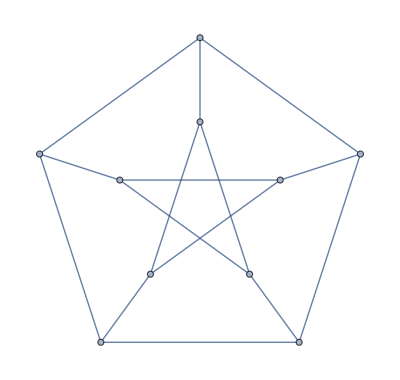

```mathematica
PetersenGraph[5,2]
```

```mathematica
TuttePolynomial[PetersenGraph[5,2],{x,y}]
```

36 x+120 x^2+180 x^3+170 x^4+114 x^5+56 x^6+21 x^7+6 x^8+x^9+36 y+168 x y+240 x^2 y+170 x^3 y+70 x^4 y+12 x^5 y+84 y^2+171 x y^2+105 x^2 y^2+30 x^3 y^2+75 y^3+65 x y^3+15 x^2 y^3+35 y^4+10 x y^4+9 y^5+y^6

```mathematica
With[{p=TuttePolynomial[PetersenGraph[5,2],{x,y}]},
Table[If[k==l==0,0,Coefficient[p,x^k y^l]],{k,0,10},{l,0,10}]//MatrixForm
]
```

(0 | 36+168 x+240 x^2+170 x^3+70 x^4+12 x^5 | 84+171 x+105 x^2+30 x^3 | 75+65 x+15 x^2 | 35+10 x | 9 | 1 | 0 | 0 | 0 | 0
36+168 y+171 y^2+65 y^3+10 y^4 | 168 | 171 | 65 | 10 | 0 | 0 | 0 | 0 | 0 | 0
120+240 y+105 y^2+15 y^3 | 240 | 105 | 15 | 0 | 0 | 0 | 0 | 0 | 0 | 0
180+170 y+30 y^2 | 170 | 30 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
170+70 y | 70 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
114+12 y | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
56 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
21 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TuttePolynomial[PetersenGraph[5,2],{0,x}]
```

36 x+84 x^2+75 x^3+35 x^4+9 x^5+x^6

```mathematica
ChromaticPolynomial[PetersenGraph[5,2],x]
```

-704 x+2606 x^2-4305 x^3+4275 x^4-2861 x^5+1353 x^6-455 x^7+105 x^8-15 x^9+x^10